Running Kawasaki dynamics simulation...

Initial configuration: {0,3,0,0,1,0,0,0,0,2}

Initial energy: 0

Final configuration: {0,2,1,3,0,0,0,0,0,0}

Final energy: -1.8

Acceptance rate: 13.%

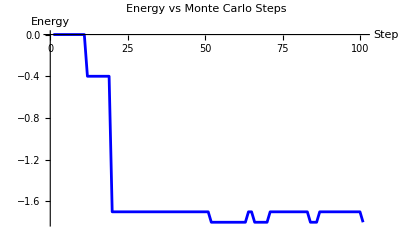

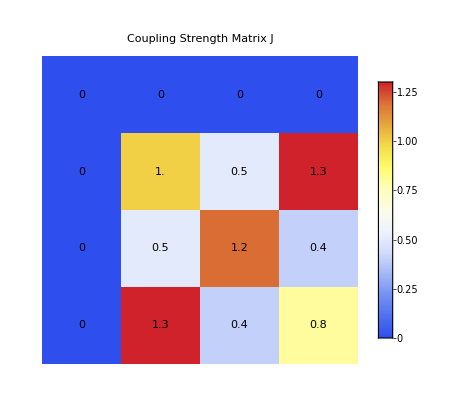

```mathematica
(*Kawasaki Dynamics on 1D Lattice*)(*Parameters*)L=10;                    (*Lattice length*)
β=10.0;                   (*Inverse temperature*)
nSteps=100;             (*Number of Monte Carlo steps*)

(*Coupling strengths-J[i,j] is coupling between particle types i and j*)
(*Type 0=empty,types 1,2,3=particles*)
JMatrix={{0,0,0,0},{0,1.0,0.5,1.3},(*J[1,1],J[1,2],J[1,3]*){0,0.5,1.2,0.4},(*J[2,1],J[2,2],J[2,3]*){0,1.3,0.4,0.8}}; (*J[3,1],J[3,2],J[3,3]*)

(*Initialize lattice with 3 particles of different types*)
(*0=empty,1,2,3=particle types*)
InitializeLattice[]:=Module[{lattice,positions},lattice=Table[0,{L}];
positions=RandomSample[Range[L],3];
lattice[[positions[[1]]]]=1;
lattice[[positions[[2]]]]=2;
lattice[[positions[[3]]]]=3;
lattice]

(*Calculate total energy with periodic boundary conditions*)
Energy[lattice_]:=Module[{E=0,i,iNext,si,siNext},Do[si=lattice[[i]];
iNext=If[i==L,1,i+1];
siNext=lattice[[iNext]];
(*Only count if both sites occupied*)If[si!=0&&siNext!=0,E+=-JMatrix[[si+1,siNext+1]]],{i,L}];
E]

(*Kawasaki step:attempt to swap two adjacent sites*)
KawasakiStep[lattice_]:=Module[{i,iNext,newLattice,ΔE,acceptProb},(*Pick random site*)i=RandomInteger[{1,L}];
iNext=If[i==L,1,i+1];
(*Only swap if sites are different*)If[lattice[[i]]==lattice[[iNext]],Return[{lattice,False}]  (*No swap,return unchanged*)];
(*Create trial configuration*)newLattice=lattice;
newLattice[[{i,iNext}]]=lattice[[{iNext,i}]];
(*Calculate energy change*)ΔE=Energy[newLattice]-Energy[lattice];
(*Metropolis acceptance criterion*)acceptProb=Min[1,Exp[-β*ΔE]];
(*Accept or reject*)If[RandomReal[]<acceptProb,{newLattice,True},(*Accept*){lattice,False}      (*Reject*)]]

(*Run simulation*)
Print["Running Kawasaki dynamics simulation..."];
lattice=InitializeLattice[];
Print["Initial configuration: ",lattice];
Print["Initial energy: ",Energy[lattice]];

energies={Energy[lattice]};
acceptances={};

Do[{lattice,accepted}=KawasakiStep[lattice];
AppendTo[energies,Energy[lattice]];
AppendTo[acceptances,If[accepted,1,0]],{nSteps}];

Print["Final configuration: ",lattice];
Print["Final energy: ",Energy[lattice]];
Print["Acceptance rate: ",N[Mean[acceptances]]*100,"%"];

(*Plot energy evolution*)
energyPlot=ListPlot[energies,PlotLabel->"Energy vs Monte Carlo Steps",AxesLabel->{"Step","Energy"},Joined->True,PlotStyle->Blue];

(*Plot J matrix with colors and values*)
jMatrixPlot=ArrayPlot[JMatrix,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"Particle Type","Particle Type"},PlotLabel->"Coupling Strength Matrix J",Epilog->Flatten[Table[Text[JMatrix[[i,j]],{j-0.5,4.5-i},BaseStyle->{FontSize->14,FontColor->If[JMatrix[[i,j]]>0.6,White,Black]}],{i,4},{j,4}]],FrameTicks->{{{{0.5,"3"},{1.5,"2"},{2.5,"1"},{3.5,"0"}},None},{{{0.5,"0"},{1.5,"1"},{2.5,"2"},{3.5,"3"}},None}}];

(*Display both plots*)
Print[energyPlot];
Print[jMatrixPlot];
```

## Doing next part with unique numbers

Running Kawasaki dynamics simulation...

Total possible configurations: 720

Generating all possible configuration IDs...

All 1000 configuration IDs:

{786432,720896,573440,536576,527360,525056,524480,524336,524300,524291,917504,458752,442368,405504,396288,393984,393408,393264,393228,393219,819200,491520,311296,307200,297984,295680,295104,294960,294924,294915,794624,466944,319488,274432,273408,271104,270528,270384,270348,270339,788480,460800,313344,276480,265216,264960,264384,264240,264204,264195,786944,459264,311808,274944,265728,262912,262848,262704,262668,262659,786560,458880,311424,274560,265344,263040,262336,262320,262284,262275,786464,458784,311328,274464,265248,262944,262368,262192,262188,262179,786440,458760,311304,274440,265224,262920,262344,262200,262156,262155,786434,458754,311298,274434,265218,262914,262338,262194,262158,262147,851968,720896,638976,602112,592896,590592,590016,589872,589836,589827,917504,196608,180224,143360,134144,131840,131264,131120,131084,131075,884736,229376,114688,110592,101376,99072,98496,98352,98316,98307,860160,204800,122880,77824,76800,74496,73920,73776,73740,73731,854016,198656,116736,79872,68608,68352,67776,67632,67596,67587,852480,197120,115200,78336,69120,66304,66240,66096,66060,66051,852096,196736,114816,77952,68736,66432,65728,65712,65676,65667,852000,196640,114720,77856,68640,66336,65760,65584,65580,65571,851976,196616,114696,77832,68616,66312,65736,65592,65548,65547,851970,196610,114690,77826,68610,66306,65730,65586,65550,65539,802816,737280,573440,552960,543744,541440,540864,540720,540684,540675,933888,212992,180224,159744,150528,148224,147648,147504,147468,147459,819200,229376,49152,45056,35840,33536,32960,32816,32780,32771,811008,221184,57344,28672,27648,25344,24768,24624,24588,24579,804864,215040,51200,30720,19456,19200,18624,18480,18444,18435,803328,213504,49664,29184,19968,17152,17088,16944,16908,16899,802944,213120,49280,28800,19584,17280,16576,16560,16524,16515,802848,213024,49184,28704,19488,17184,16608,16432,16428,16419,802824,213000,49160,28680,19464,17160,16584,16440,16396,16395,802818,212994,49154,28674,19458,17154,16578,16434,16398,16387,790528,724992,577536,536576,531456,529152,528576,528432,528396,528387,921600,200704,184320,143360,138240,135936,135360,135216,135180,135171,823296,233472,53248,45056,39936,37632,37056,36912,36876,36867,794624,204800,57344,12288,11264,8960,8384,8240,8204,8195,792576,202752,55296,14336,7168,6912,6336,6192,6156,6147,791040,201216,53760,12800,7680,4864,4800,4656,4620,4611,790656,200832,53376,12416,7296,4992,4288,4272,4236,4227,790560,200736,53280,12320,7200,4896,4320,4144,4140,4131,790536,200712,53256,12296,7176,4872,4296,4152,4108,4107,790530,200706,53250,12290,7170,4866,4290,4146,4110,4099,787456,721920,574464,537600,527360,526080,525504,525360,525324,525315,918528,197632,181248,144384,134144,132864,132288,132144,132108,132099,820224,230400,50176,46080,35840,34560,33984,33840,33804,33795,795648,205824,58368,13312,11264,9984,9408,9264,9228,9219,788480,198656,51200,14336,3072,2816,2240,2096,2060,2051,787968,198144,50688,13824,3584,1792,1728,1584,1548,1539,787584,197760,50304,13440,3200,1920,1216,1200,1164,1155,787488,197664,50208,13344,3104,1824,1248,1072,1068,1059,787464,197640,50184,13320,3080,1800,1224,1080,1036,1035,787458,197634,50178,13314,3074,1794,1218,1074,1038,1027,786688,721152,573696,536832,527616,525056,524736,524592,524556,524547,917760,196864,180480,143616,134400,131840,131520,131376,131340,131331,819456,229632,49408,45312,36096,33536,33216,33072,33036,33027,794880,205056,57600,12544,11520,8960,8640,8496,8460,8451,788736,198912,51456,14592,3328,2816,2496,2352,2316,2307,786944,197120,49664,12800,3584,768,704,560,524,515,786816,196992,49536,12672,3456,896,448,432,396,387,786720,196896,49440,12576,3360,800,480,304,300,291,786696,196872,49416,12552,3336,776,456,312,268,267,786690,196866,49410,12546,3330,770,450,306,270,259,786496,720960,573504,536640,527424,525120,524480,524400,524364,524355,917568,196672,180288,143424,134208,131904,131264,131184,131148,131139,819264,229440,49216,45120,35904,33600,32960,32880,32844,32835,794688,204864,57408,12352,11328,9024,8384,8304,8268,8259,788544,198720,51264,14400,3136,2880,2240,2160,2124,2115,787008,197184,49728,12864,3648,832,704,624,588,579,786560,196736,49280,12416,3200,896,192,176,140,131,786528,196704,49248,12384,3168,864,224,112,108,99,786504,196680,49224,12360,3144,840,200,120,76,75,786498,196674,49218,12354,3138,834,194,114,78,67,786448,720912,573456,536592,527376,525072,524496,524336,524316,524307,917520,196624,180240,143376,134160,131856,131280,131120,131100,131091,819216,229392,49168,45072,35856,33552,32976,32816,32796,32787,794640,204816,57360,12304,11280,8976,8400,8240,8220,8211,788496,198672,51216,14352,3088,2832,2256,2096,2076,2067,786960,197136,49680,12816,3600,784,720,560,540,531,786576,196752,49296,12432,3216,912,208,176,156,147,786464,196640,49184,12320,3104,800,224,48,44,35,786456,196632,49176,12312,3096,792,216,56,28,27,786450,196626,49170,12306,3090,786,210,50,30,19,786436,720900,573444,536580,527364,525060,524484,524340,524300,524295,917508,196612,180228,143364,134148,131844,131268,131124,131084,131079,819204,229380,49156,45060,35844,33540,32964,32820,32780,32775,794628,204804,57348,12292,11268,8964,8388,8244,8204,8199,788484,198660,51204,14340,3076,2820,2244,2100,2060,2055,786948,197124,49668,12804,3588,772,708,564,524,519,786564,196740,49284,12420,3204,900,196,180,140,135,786468,196644,49188,12324,3108,804,228,52,44,39,786440,196616,49160,12296,3080,776,200,56,12,11,786438,196614,49158,12294,3078,774,198,54,14,7,786433,720897,573441,536577,527361,525057,524481,524337,524301,524291,917505,196609,180225,143361,134145,131841,131265,131121,131085,131075,819201,229377,49153,45057,35841,33537,32961,32817,32781,32771,794625,204801,57345,12289,11265,8961,8385,8241,8205,8195,788481,198657,51201,14337,3073,2817,2241,2097,2061,2051,786945,197121,49665,12801,3585,769,705,561,525,515,786561,196737,49281,12417,3201,897,193,177,141,131,786465,196641,49185,12321,3105,801,225,49,45,35,786441,196617,49161,12297,3081,777,201,57,13,11,786434,196610,49154,12290,3074,770,194,50,14,3}

Initial configuration: {1,3,0,2,0,0,0,0,0,0}

Initial configuration ID: 466944

Initial energy: -0.3

Final configuration: {0,0,0,0,0,3,1,0,0,2}

Final configuration ID: 834

Final energy: -0.3

Acceptance rate: 47.1%

Unique configurations visited: 640

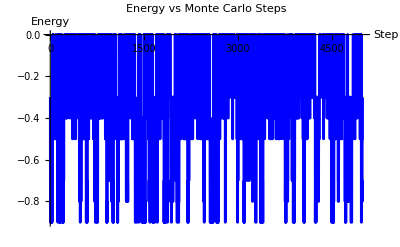

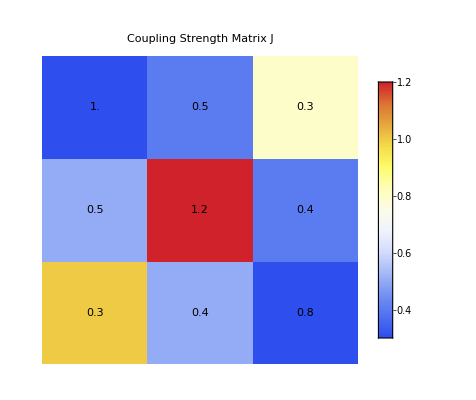

```mathematica
(*Kawasaki Dynamics on 1D Lattice*)(*Parameters*)L=10;                    (*Lattice length*)
β=1.0;                   (*Inverse temperature*)
nSteps=5000;             (*Number of Monte Carlo steps*)

(*Coupling strengths-J[i,j] is coupling between particle types i and j*)
(*Type 0=empty,types 1,2,3=particles*)
JMatrix={{0,0,0,0},{0,1.0,0.5,0.3},(*J[1,1],J[1,2],J[1,3]*){0,0.5,1.2,0.4},(*J[2,1],J[2,2],J[2,3]*){0,0.3,0.4,0.8}}; (*J[3,1],J[3,2],J[3,3]*)

(*Initialize lattice with 3 particles of different types*)
(*0=empty,1,2,3=particle types*)
InitializeLattice[]:=Module[{lattice,positions},lattice=Table[0,{L}];
positions=RandomSample[Range[L],3];
lattice[[positions[[1]]]]=1;
lattice[[positions[[2]]]]=2;
lattice[[positions[[3]]]]=3;
lattice]

(*Numbering scheme:convert lattice configuration to unique ID*)
(*Each site can be 0,1,2,3 so we use base-4 representation*)
LatticeToID[lattice_]:=FromDigits[lattice,4]

(*Convert ID back to lattice configuration*)
IDToLattice[id_,L_]:=IntegerDigits[id,4,L]

(*Generate all possible configurations*)
GenerateAllConfigs[L_]:=Module[{configs,positions},configs={};
Do[(*pos1,pos2,pos3 are positions of particles 1,2,3*)Module[{lattice},lattice=Table[0,{L}];
lattice[[pos1]]=1;
lattice[[pos2]]=2;
lattice[[pos3]]=3;
AppendTo[configs,lattice]],{pos1,L},{pos2,L},{pos3,L}]/;pos1!=pos2&&pos2!=pos3&&pos1!=pos3;
configs]

(*Get all valid configuration IDs*)
GetAllConfigIDs[L_]:=Module[{allConfigs},allConfigs=GenerateAllConfigs[L];
LatticeToID/@allConfigs]

(*Calculate total energy with periodic boundary conditions*)
Energy[lattice_]:=Module[{E=0,i,iNext,si,siNext},Do[si=lattice[[i]];
iNext=If[i==L,1,i+1];
siNext=lattice[[iNext]];
(*Only count if both sites occupied*)If[si!=0&&siNext!=0,E+=-JMatrix[[si+1,siNext+1]]],{i,L}];
E]

(*Kawasaki step:attempt to swap two adjacent sites*)
KawasakiStep[lattice_]:=Module[{i,iNext,newLattice,ΔE,acceptProb},(*Pick random site*)i=RandomInteger[{1,L}];
iNext=If[i==L,1,i+1];
(*Only swap if sites are different*)If[lattice[[i]]==lattice[[iNext]],Return[{lattice,False}]  (*No swap,return unchanged*)];
(*Create trial configuration*)newLattice=lattice;
newLattice[[{i,iNext}]]=lattice[[{iNext,i}]];
(*Calculate energy change*)ΔE=Energy[newLattice]-Energy[lattice];
(*Metropolis acceptance criterion*)acceptProb=Min[1,Exp[-β*ΔE]];
(*Accept or reject*)If[RandomReal[]<acceptProb,{newLattice,True},(*Accept*){lattice,False}      (*Reject*)]]

(*Run simulation*)
Print["Running Kawasaki dynamics simulation..."];
Print["Total possible configurations: ",L*(L-1)*(L-2)];

(*Generate and print all configuration IDs*)
Print["Generating all possible configuration IDs..."];
allIDs=GetAllConfigIDs[L];
Print["All ",Length[allIDs]," configuration IDs:"];
Print[allIDs];

lattice=InitializeLattice[];
Print["Initial configuration: ",lattice];
Print["Initial configuration ID: ",LatticeToID[lattice]];
Print["Initial energy: ",Energy[lattice]];

energies={Energy[lattice]};
acceptances={};
configIDs={LatticeToID[lattice]};

Do[{lattice,accepted}=KawasakiStep[lattice];
AppendTo[energies,Energy[lattice]];
AppendTo[acceptances,If[accepted,1,0]];
AppendTo[configIDs,LatticeToID[lattice]],{nSteps}];

Print["Final configuration: ",lattice];
Print["Final configuration ID: ",LatticeToID[lattice]];
Print["Final energy: ",Energy[lattice]];
Print["Acceptance rate: ",N[Mean[acceptances]]*100,"%"];
Print["Unique configurations visited: ",Length[DeleteDuplicates[configIDs]]];

(*Plot energy evolution*)
energyPlot=ListPlot[energies,PlotLabel->"Energy vs Monte Carlo Steps",AxesLabel->{"Step","Energy"},Joined->True,PlotStyle->Blue];

(*Plot J matrix with colors and values*)
(*Extract only the particle-particle couplings (exclude empty site row/col)*)
JParticles=JMatrix[[2;;4,2;;4]];

jMatrixPlot=ArrayPlot[JParticles,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"Particle Type","Particle Type"},PlotLabel->"Coupling Strength Matrix J",Epilog->Flatten[Table[Text[JParticles[[i,j]],{j-0.5,3.5-i},BaseStyle->{FontSize->14,FontColor->If[JParticles[[i,j]]>Mean[Flatten[JParticles]],White,Black]}],{i,3},{j,3}]],FrameTicks->{{{{0.5,"3"},{1.5,"2"},{2.5,"1"}},None},{{{0.5,"1"},{1.5,"2"},{2.5,"3"}},None}},DataReversed->True];

(*Display both plots*)
Print[energyPlot];
Print[jMatrixPlot];
```

## Plotting against Boltzmann

Running Kawasaki dynamics simulation...

Total possible configurations: 720

Generating all possible configurations...

Calculating Boltzmann probabilities...

Number of unique configurations: 1000

Energy range: -0.9 to 0

Initial configuration: {1,0,3,2,0,0,0,0,0,0}

Initial configuration ID: 319488

Initial energy: -0.4

Final configuration: {0,3,0,2,0,0,0,1,0,0}

Final configuration ID: 204816

Final energy: 0

Acceptance rate: 47.188%

Unique configurations visited: 720

Calculating observed frequencies...

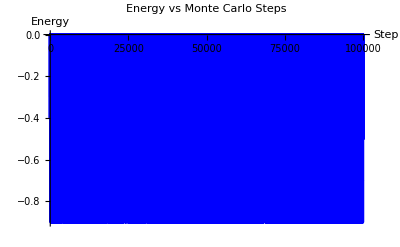

-Graphics-

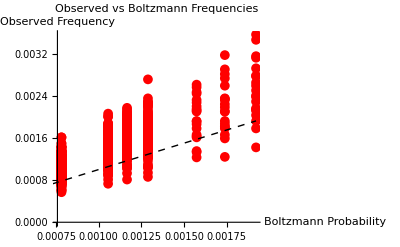

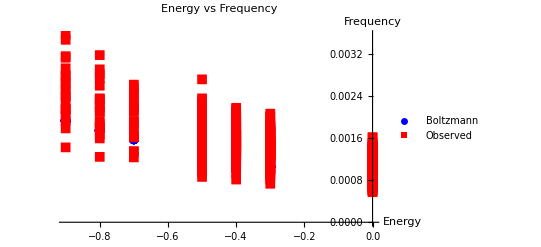

```mathematica
(*Kawasaki Dynamics on 1D Lattice*)(*Parameters*)L=10;                    (*Lattice length*)
β=1.0;                   (*Inverse temperature*)
nSteps=100000;             (*Number of Monte Carlo steps*)

(*Coupling strengths-J[i,j] is coupling between particle types i and j*)
(*Type 0=empty,types 1,2,3=particles*)
JMatrix={{0,0,0,0},{0,1.0,0.5,0.3},(*J[1,1],J[1,2],J[1,3]*){0,0.5,1.2,0.4},(*J[2,1],J[2,2],J[2,3]*){0,0.3,0.4,0.8}}; (*J[3,1],J[3,2],J[3,3]*)

(*Initialize lattice with 3 particles of different types*)
(*0=empty,1,2,3=particle types*)
InitializeLattice[]:=Module[{lattice,positions},lattice=Table[0,{L}];
positions=RandomSample[Range[L],3];
lattice[[positions[[1]]]]=1;
lattice[[positions[[2]]]]=2;
lattice[[positions[[3]]]]=3;
lattice]

(*Numbering scheme:convert lattice configuration to unique ID*)
(*Each site can be 0,1,2,3 so we use base-4 representation*)
LatticeToID[lattice_]:=FromDigits[lattice,4]

(*Convert ID back to lattice configuration*)
IDToLattice[id_,L_]:=IntegerDigits[id,4,L]

(*Generate all possible configurations*)
GenerateAllConfigs[L_]:=Module[{configs,positions},configs={};
Do[(*pos1,pos2,pos3 are positions of particles 1,2,3*)Module[{lattice},lattice=Table[0,{L}];
lattice[[pos1]]=1;
lattice[[pos2]]=2;
lattice[[pos3]]=3;
AppendTo[configs,lattice]],{pos1,L},{pos2,L},{pos3,L}]/;pos1!=pos2&&pos2!=pos3&&pos1!=pos3;
configs]

(*Get all valid configuration IDs*)
GetAllConfigIDs[L_]:=Module[{allConfigs},allConfigs=GenerateAllConfigs[L];
LatticeToID/@allConfigs]

(*Calculate total energy with periodic boundary conditions*)
Energy[lattice_]:=Module[{E=0,i,iNext,si,siNext},Do[si=lattice[[i]];
iNext=If[i==L,1,i+1];
siNext=lattice[[iNext]];
(*Only count if both sites occupied*)If[si!=0&&siNext!=0,E+=-JMatrix[[si+1,siNext+1]]],{i,L}];
E]

(*Kawasaki step:attempt to swap two adjacent sites*)
KawasakiStep[lattice_]:=Module[{i,iNext,newLattice,ΔE,acceptProb},(*Pick random site*)i=RandomInteger[{1,L}];
iNext=If[i==L,1,i+1];
(*Only swap if sites are different*)If[lattice[[i]]==lattice[[iNext]],Return[{lattice,False}]  (*No swap,return unchanged*)];
(*Create trial configuration*)newLattice=lattice;
newLattice[[{i,iNext}]]=lattice[[{iNext,i}]];
(*Calculate energy change*)ΔE=Energy[newLattice]-Energy[lattice];
(*Metropolis acceptance criterion*)acceptProb=Min[1,Exp[-β*ΔE]];
(*Accept or reject*)If[RandomReal[]<acceptProb,{newLattice,True},(*Accept*){lattice,False}      (*Reject*)]]

(*Run simulation*)
Print["Running Kawasaki dynamics simulation..."];
Print["Total possible configurations: ",L*(L-1)*(L-2)];

(*Generate all configurations and calculate their properties*)
Print["Generating all possible configurations..."];
allConfigs=GenerateAllConfigs[L];
allIDs=LatticeToID/@allConfigs;
allEnergies=Energy/@allConfigs;

Print["Calculating Boltzmann probabilities..."];
(*Boltzmann probabilities*)
boltzmannWeights=Exp[-β*allEnergies];
partitionFunction=Total[boltzmannWeights];
boltzmannProbs=boltzmannWeights/partitionFunction;

(*Create lookup table:ID->{energy,Boltzmann probability}*)
configData=Association[MapThread[#1->{#2,#3}&,{allIDs,allEnergies,boltzmannProbs}]];

Print["Number of unique configurations: ",Length[allIDs]];
Print["Energy range: ",Min[allEnergies]," to ",Max[allEnergies]];

lattice=InitializeLattice[];
Print["Initial configuration: ",lattice];
Print["Initial configuration ID: ",LatticeToID[lattice]];
Print["Initial energy: ",Energy[lattice]];

energies={Energy[lattice]};
acceptances={};
configIDs={LatticeToID[lattice]};

Do[{lattice,accepted}=KawasakiStep[lattice];
AppendTo[energies,Energy[lattice]];
AppendTo[acceptances,If[accepted,1,0]];
AppendTo[configIDs,LatticeToID[lattice]],{nSteps}];

Print["Final configuration: ",lattice];
Print["Final configuration ID: ",LatticeToID[lattice]];
Print["Final energy: ",Energy[lattice]];
Print["Acceptance rate: ",N[Mean[acceptances]]*100,"%"];
Print["Unique configurations visited: ",Length[DeleteDuplicates[configIDs]]];

(*Calculate observed frequencies*)
Print["\nCalculating observed frequencies..."];
visitCounts=Counts[configIDs];
totalVisits=Length[configIDs];
observedFreqs=Association[#->visitCounts[#]/totalVisits&/@Keys[visitCounts]];

(*Prepare data for plotting*)
(*Only plot configurations that were actually visited*)
visitedIDs=Keys[visitCounts];
boltzmannFreqs=configData[#][[2]]&/@visitedIDs;
observedFreqsList=observedFreqs[#]&/@visitedIDs;

(*Create comparison plot*)
comparisonPlot=ListPlot[{Transpose[{boltzmannFreqs,observedFreqsList}]},PlotLabel->"Observed vs Boltzmann Frequencies",AxesLabel->{"Boltzmann Probability","Observed Frequency"},PlotStyle->{Red},PlotMarkers->{Automatic,Medium},Epilog->{Dashed,Line[{{0,0},{Max[boltzmannFreqs],Max[boltzmannFreqs]}}]}];

(*Plot energy vs frequency for both*)
energyFreqPlot=ListPlot[{Transpose[{configData[#][[1]]&/@visitedIDs,boltzmannFreqs}],Transpose[{configData[#][[1]]&/@visitedIDs,observedFreqsList}]},PlotLabel->"Energy vs Frequency",AxesLabel->{"Energy","Frequency"},PlotStyle->{Blue,Red},PlotLegends->{"Boltzmann","Observed"},PlotMarkers->{Automatic,Medium}];

(*Plot energy evolution*)
energyPlot=ListPlot[energies,PlotLabel->"Energy vs Monte Carlo Steps",AxesLabel->{"Step","Energy"},Joined->True,PlotStyle->Blue];

(*Plot J matrix with colors and values*)
(*Extract only the particle-particle couplings (exclude empty site row/col)*)
JParticles=JMatrix[[2;;4,2;;4]];

jMatrixPlot=ArrayPlot[JParticles,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"Particle Type","Particle Type"},PlotLabel->"Coupling Strength Matrix J",Epilog->Flatten[Table[Text[JParticles[[i,j]],{j-0.5,3.5-i},BaseStyle->{FontSize->14,FontColor->If[JParticles[[i,j]]>Mean[Flatten[JParticles]],White,Black]}],{i,3},{j,3}]],FrameTicks->{{{{0.5,"3"},{1.5,"2"},{2.5,"1"}},None},{{{0.5,"1"},{1.5,"2"},{2.5,"3"}},None}},DataReversed->True];

(*Display all plots*)
Print[energyPlot];
Print[jMatrixPlot];
Print[comparisonPlot];
Print[energyFreqPlot];
```

## Multiple particles

Coupling matrix J (5x5):

(0 | 0 | 0 | 0 | 0
0 | 1.12418 | 1.48956 | 1.35146 | 0.78715
0 | 1.48956 | 0.950879 | 1.17102 | 0.309682
0 | 1.35146 | 1.17102 | 1.1979 | 1.45616
0 | 0.78715 | 0.309682 | 1.45616 | 0.779915)

Running Kawasaki dynamics simulation...

Total possible configurations: 120

Generating all possible configurations...

Calculating Boltzmann probabilities...

Number of unique configurations: 120

Energy range: -4.29718 to -2.26785

Initial configuration: {1,3,0,4,2}

Initial configuration ID: 1022

Initial energy: -3.15071

Final configuration: {3,4,0,2,1}

Final configuration ID: 2386

Final energy: -4.29718

Acceptance rate: 70.257%

Unique configurations visited: 120

Calculating observed frequencies...

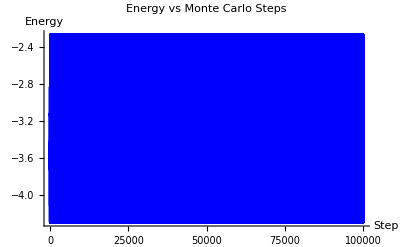

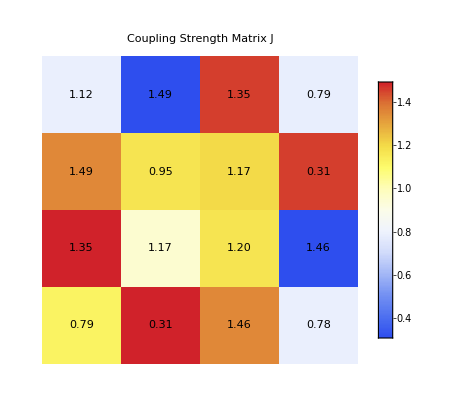

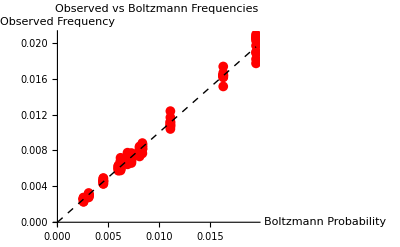

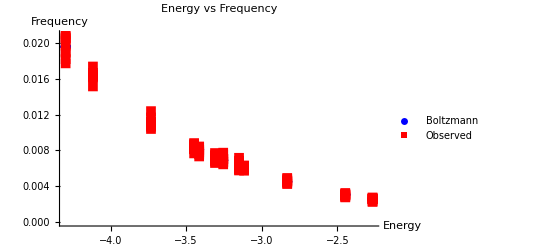

```mathematica
(*Kawasaki Dynamics on 1D Lattice*)(*Parameters*)L=5;                    (*Lattice length*)
nParticles=4;            (*Number of particles on lattice*)
β=1.0;                   (*Inverse temperature*)
nSteps=100000;             (*Number of Monte Carlo steps*)

(*Generate coupling matrix for nParticles particle types*)
(*J[i,j] is coupling between particle types i and j*)
(*Type 0=empty,types 1,2,...,nParticles=particles*)
GenerateJMatrix[nParticles_]:=Module[{J,i,j},J=Table[0,{nParticles+1},{nParticles+1}];
(*Fill in couplings between particle types*)Do[Do[(*Generate random coupling strength between 0.3 and 1.5*)J[[i+1,j+1]]=RandomReal[{0.3,1.5}];
J[[j+1,i+1]]=J[[i+1,j+1]],(*Symmetric*){j,i,nParticles}],{i,1,nParticles}];
J]

JMatrix=GenerateJMatrix[nParticles];
Print["Coupling matrix J (",nParticles+1,"x",nParticles+1,"):"];
Print[JMatrix//MatrixForm];

(*Initialize lattice with nParticles particles of different types*)
(*0=empty,1,2,...,nParticles=particle types*)
InitializeLattice[]:=Module[{lattice,positions},lattice=Table[0,{L}];
positions=RandomSample[Range[L],nParticles];
Do[lattice[[positions[[i]]]]=i,{i,nParticles}];
lattice]

(*Numbering scheme:convert lattice configuration to unique ID*)
(*Each site can be 0,1,2,...,nParticles so we use base-(nParticles+1) representation*)
LatticeToID[lattice_]:=FromDigits[lattice,nParticles+1]

(*Convert ID back to lattice configuration*)
IDToLattice[id_,L_]:=IntegerDigits[id,nParticles+1,L]

(*Generate all possible configurations*)
GenerateAllConfigs[L_]:=Module[{configs,positions,lattice},configs={};
(*Generate all permutations of nParticles particles on L sites*)Do[lattice=Table[0,{L}];
Do[lattice[[positions[[i]]]]=i,{i,nParticles}];
AppendTo[configs,lattice],{positions,Subsets[Range[L],{nParticles}]}];
(*For each position set,generate all permutations of particle labels*)Flatten[Table[lattice=Table[0,{L}];
Do[lattice[[positions[[i]]]]=perm[[i]],{i,nParticles}];
lattice,{positions,Subsets[Range[L],{nParticles}]},{perm,Permutations[Range[nParticles]]}],1]]

(*Get all valid configuration IDs*)
GetAllConfigIDs[L_]:=Module[{allConfigs},allConfigs=GenerateAllConfigs[L];
LatticeToID/@allConfigs]

(*Calculate total energy with periodic boundary conditions*)
Energy[lattice_]:=Module[{E=0,i,iNext,si,siNext},Do[si=lattice[[i]];
iNext=If[i==L,1,i+1];
siNext=lattice[[iNext]];
(*Only count if both sites occupied*)If[si!=0&&siNext!=0,E+=-JMatrix[[si+1,siNext+1]]],{i,L}];
E]

(*Kawasaki step:attempt to swap two adjacent sites*)
KawasakiStep[lattice_]:=Module[{i,iNext,newLattice,ΔE,acceptProb},(*Pick random site*)i=RandomInteger[{1,L}];
iNext=If[i==L,1,i+1];
(*Only swap if sites are different*)If[lattice[[i]]==lattice[[iNext]],Return[{lattice,False}]  (*No swap,return unchanged*)];
(*Create trial configuration*)newLattice=lattice;
newLattice[[{i,iNext}]]=lattice[[{iNext,i}]];
(*Calculate energy change*)ΔE=Energy[newLattice]-Energy[lattice];
(*Metropolis acceptance criterion*)acceptProb=Min[1,Exp[-β*ΔE]];
(*Accept or reject*)If[RandomReal[]<acceptProb,{newLattice,True},(*Accept*){lattice,False}      (*Reject*)]]

(*Run simulation*)
Print["\nRunning Kawasaki dynamics simulation..."];
Print["Total possible configurations: ",Binomial[L,nParticles]*Factorial[nParticles]];

(*Generate all configurations and calculate their properties*)
Print["Generating all possible configurations..."];
allConfigs=GenerateAllConfigs[L];
allIDs=LatticeToID/@allConfigs;
allEnergies=Energy/@allConfigs;

Print["Calculating Boltzmann probabilities..."];
(*Boltzmann probabilities*)
boltzmannWeights=Exp[-β*allEnergies];
partitionFunction=Total[boltzmannWeights];
boltzmannProbs=boltzmannWeights/partitionFunction;

(*Create lookup table:ID->{energy,Boltzmann probability}*)
configData=Association[MapThread[#1->{#2,#3}&,{allIDs,allEnergies,boltzmannProbs}]];

Print["Number of unique configurations: ",Length[allIDs]];
Print["Energy range: ",Min[allEnergies]," to ",Max[allEnergies]];

lattice=InitializeLattice[];
Print["Initial configuration: ",lattice];
Print["Initial configuration ID: ",LatticeToID[lattice]];
Print["Initial energy: ",Energy[lattice]];

energies={Energy[lattice]};
acceptances={};
configIDs={LatticeToID[lattice]};

Do[{lattice,accepted}=KawasakiStep[lattice];
AppendTo[energies,Energy[lattice]];
AppendTo[acceptances,If[accepted,1,0]];
AppendTo[configIDs,LatticeToID[lattice]],{nSteps}];

Print["Final configuration: ",lattice];
Print["Final configuration ID: ",LatticeToID[lattice]];
Print["Final energy: ",Energy[lattice]];
Print["Acceptance rate: ",N[Mean[acceptances]]*100,"%"];
Print["Unique configurations visited: ",Length[DeleteDuplicates[configIDs]]];

(*Calculate observed frequencies*)
Print["\nCalculating observed frequencies..."];
visitCounts=Counts[configIDs];
totalVisits=Length[configIDs];
observedFreqs=Association[#->visitCounts[#]/totalVisits&/@Keys[visitCounts]];

(*Prepare data for plotting*)
(*Only plot configurations that were actually visited*)
visitedIDs=Keys[visitCounts];
boltzmannFreqs=configData[#][[2]]&/@visitedIDs;
observedFreqsList=observedFreqs[#]&/@visitedIDs;

(*Create comparison plot*)
comparisonPlot=ListPlot[{Transpose[{boltzmannFreqs,observedFreqsList}]},PlotLabel->"Observed vs Boltzmann Frequencies",AxesLabel->{"Boltzmann Probability","Observed Frequency"},PlotStyle->{Red},PlotMarkers->{Automatic,Medium},Epilog->{Dashed,Line[{{0,0},{Max[boltzmannFreqs],Max[boltzmannFreqs]}}]}];

(*Plot energy vs frequency for both*)
energyFreqPlot=ListPlot[{Transpose[{configData[#][[1]]&/@visitedIDs,boltzmannFreqs}],Transpose[{configData[#][[1]]&/@visitedIDs,observedFreqsList}]},PlotLabel->"Energy vs Frequency",AxesLabel->{"Energy","Frequency"},PlotStyle->{Blue,Red},PlotLegends->{"Boltzmann","Observed"},PlotMarkers->{Automatic,Medium}];

(*Plot energy evolution*)
energyPlot=ListPlot[energies,PlotLabel->"Energy vs Monte Carlo Steps",AxesLabel->{"Step","Energy"},Joined->True,PlotStyle->Blue];

(*Plot J matrix with colors and values*)
(*Extract only the particle-particle couplings (exclude empty site row/col)*)
JParticles=JMatrix[[2;;nParticles+1,2;;nParticles+1]];

jMatrixPlot=ArrayPlot[JParticles,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"Particle Type","Particle Type"},PlotLabel->"Coupling Strength Matrix J",Epilog->Flatten[Table[Text[NumberForm[JParticles[[i,j]],{3,2}],{j-0.5,nParticles+0.5-i},BaseStyle->{FontSize->12,FontColor->If[JParticles[[i,j]]>Mean[Flatten[JParticles]],White,Black]}],{i,nParticles},{j,nParticles}]],FrameTicks->{{Table[{i-0.5,ToString[nParticles+1-i]},{i,nParticles}],None},{Table[{i-0.5,ToString[i]},{i,nParticles}],None}},DataReversed->True];

(*Display all plots*)
Print[energyPlot];
Print[jMatrixPlot];
Print[comparisonPlot];
Print[energyFreqPlot];
```

## Transition Matrix Plotting

Coupling matrix J (5x5):

(0 | 0 | 0 | 0 | 0
0 | 1.4296 | 1.09938 | 0.851222 | 1.26312
0 | 1.09938 | 0.615243 | 0.917901 | 0.582269
0 | 0.851222 | 0.917901 | 0.56732 | 0.984451
0 | 1.26312 | 0.582269 | 0.984451 | 0.55653)

Running Kawasaki dynamics simulation...

Total possible configurations: 120

Generating all possible configurations...

Calculating Boltzmann probabilities...

Number of unique configurations: 120

Energy range: -3.34695 to -2.35139

Initial configuration: {4,1,0,3,2}

Initial configuration ID: 2642

Initial energy: -2.76329

Final configuration: {4,3,0,2,1}

Final configuration ID: 2886

Final energy: -3.34695

Acceptance rate: 83.28%

Unique configurations visited: 120

Calculating observed frequencies...

Building empirical transition matrix...

Empirical transition matrix size: 120x120

Sample transition probabilities (first 5x5):

(6/47 | 8/47 | 3/47 | 0 | 0
14/37 | 6/37 | 0 | 0 | 7/37
5/22 | 0 | 0 | 1/22 | 0
0 | 0 | 5/28 | 0 | 0
0 | 3/22 | 0 | 0 | 3/22)

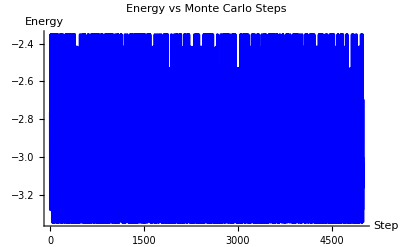

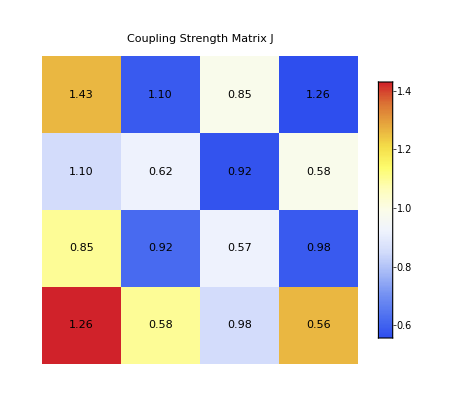

-Graphics-

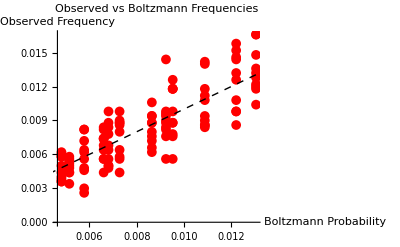

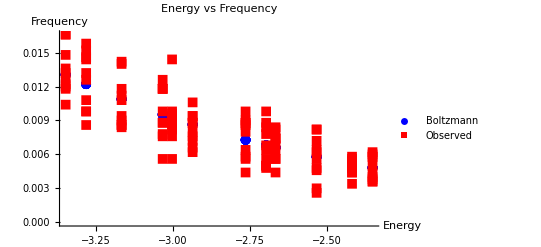

```mathematica
(*Kawasaki Dynamics on 1D Lattice*)(*Parameters*)L=5;                    (*Lattice length*)
nParticles=4;            (*Number of particles on lattice*)
β=1.0;                   (*Inverse temperature*)
nSteps=5000;             (*Number of Monte Carlo steps*)

(*Generate coupling matrix for nParticles particle types*)
(*J[i,j] is coupling between particle types i and j*)
(*Type 0=empty,types 1,2,...,nParticles=particles*)
GenerateJMatrix[nParticles_]:=Module[{J,i,j},J=Table[0,{nParticles+1},{nParticles+1}];
(*Fill in couplings between particle types*)Do[Do[(*Generate random coupling strength between 0.3 and 1.5*)J[[i+1,j+1]]=RandomReal[{0.3,1.5}];
J[[j+1,i+1]]=J[[i+1,j+1]],(*Symmetric*){j,i,nParticles}],{i,1,nParticles}];
J]

JMatrix=GenerateJMatrix[nParticles];
Print["Coupling matrix J (",nParticles+1,"x",nParticles+1,"):"];
Print[JMatrix//MatrixForm];

(*Initialize lattice with nParticles particles of different types*)
(*0=empty,1,2,...,nParticles=particle types*)
InitializeLattice[]:=Module[{lattice,positions},lattice=Table[0,{L}];
positions=RandomSample[Range[L],nParticles];
Do[lattice[[positions[[i]]]]=i,{i,nParticles}];
lattice]

(*Numbering scheme:convert lattice configuration to unique ID*)
(*Each site can be 0,1,2,...,nParticles so we use base-(nParticles+1) representation*)
LatticeToID[lattice_]:=FromDigits[lattice,nParticles+1]

(*Convert ID back to lattice configuration*)
IDToLattice[id_,L_]:=IntegerDigits[id,nParticles+1,L]

(*Generate all possible configurations*)
GenerateAllConfigs[L_]:=Module[{configs,positions,lattice},configs={};
(*Generate all permutations of nParticles particles on L sites*)Do[lattice=Table[0,{L}];
Do[lattice[[positions[[i]]]]=i,{i,nParticles}];
AppendTo[configs,lattice],{positions,Subsets[Range[L],{nParticles}]}];
(*For each position set,generate all permutations of particle labels*)Flatten[Table[lattice=Table[0,{L}];
Do[lattice[[positions[[i]]]]=perm[[i]],{i,nParticles}];
lattice,{positions,Subsets[Range[L],{nParticles}]},{perm,Permutations[Range[nParticles]]}],1]]

(*Get all valid configuration IDs*)
GetAllConfigIDs[L_]:=Module[{allConfigs},allConfigs=GenerateAllConfigs[L];
LatticeToID/@allConfigs]

(*Calculate total energy with periodic boundary conditions*)
Energy[lattice_]:=Module[{E=0,i,iNext,si,siNext},Do[si=lattice[[i]];
iNext=If[i==L,1,i+1];
siNext=lattice[[iNext]];
(*Only count if both sites occupied*)If[si!=0&&siNext!=0,E+=-JMatrix[[si+1,siNext+1]]],{i,L}];
E]

(*Kawasaki step:attempt to swap two adjacent sites*)
KawasakiStep[lattice_]:=Module[{i,iNext,newLattice,ΔE,acceptProb},(*Pick random site*)i=RandomInteger[{1,L}];
iNext=If[i==L,1,i+1];
(*Only swap if sites are different*)If[lattice[[i]]==lattice[[iNext]],Return[{lattice,False}]  (*No swap,return unchanged*)];
(*Create trial configuration*)newLattice=lattice;
newLattice[[{i,iNext}]]=lattice[[{iNext,i}]];
(*Calculate energy change*)ΔE=Energy[newLattice]-Energy[lattice];
(*Metropolis acceptance criterion*)acceptProb=Min[1,Exp[-β*ΔE]];
(*Accept or reject*)If[RandomReal[]<acceptProb,{newLattice,True},(*Accept*){lattice,False}      (*Reject*)]]

(*Run simulation*)
Print["\nRunning Kawasaki dynamics simulation..."];
Print["Total possible configurations: ",Binomial[L,nParticles]*Factorial[nParticles]];

(*Generate all configurations and calculate their properties*)
Print["Generating all possible configurations..."];
allConfigs=GenerateAllConfigs[L];
allIDs=LatticeToID/@allConfigs;
allEnergies=Energy/@allConfigs;

Print["Calculating Boltzmann probabilities..."];
(*Boltzmann probabilities*)
boltzmannWeights=Exp[-β*allEnergies];
partitionFunction=Total[boltzmannWeights];
boltzmannProbs=boltzmannWeights/partitionFunction;

(*Create lookup table:ID->{energy,Boltzmann probability}*)
configData=Association[MapThread[#1->{#2,#3}&,{allIDs,allEnergies,boltzmannProbs}]];

Print["Number of unique configurations: ",Length[allIDs]];
Print["Energy range: ",Min[allEnergies]," to ",Max[allEnergies]];

lattice=InitializeLattice[];
Print["Initial configuration: ",lattice];
Print["Initial configuration ID: ",LatticeToID[lattice]];
Print["Initial energy: ",Energy[lattice]];

energies={Energy[lattice]};
acceptances={};
configIDs={LatticeToID[lattice]};

Do[{lattice,accepted}=KawasakiStep[lattice];
AppendTo[energies,Energy[lattice]];
AppendTo[acceptances,If[accepted,1,0]];
AppendTo[configIDs,LatticeToID[lattice]],{nSteps}];

Print["Final configuration: ",lattice];
Print["Final configuration ID: ",LatticeToID[lattice]];
Print["Final energy: ",Energy[lattice]];
Print["Acceptance rate: ",N[Mean[acceptances]]*100,"%"];
Print["Unique configurations visited: ",Length[DeleteDuplicates[configIDs]]];

(*Calculate observed frequencies*)
Print["\nCalculating observed frequencies..."];
visitCounts=Counts[configIDs];
totalVisits=Length[configIDs];
observedFreqs=Association[#->visitCounts[#]/totalVisits&/@Keys[visitCounts]];

(*Build empirical transition matrix*)
Print["Building empirical transition matrix..."];
visitedIDs=Sort[Keys[visitCounts]];
nVisited=Length[visitedIDs];
idToIndex=Association[MapThread[Rule,{visitedIDs,Range[nVisited]}]];

(*Count transitions*)
transitionCounts=Table[0,{nVisited},{nVisited}];
Do[fromID=configIDs[[t]];
toID=configIDs[[t+1]];
If[KeyExistsQ[idToIndex,fromID]&&KeyExistsQ[idToIndex,toID],fromIdx=idToIndex[fromID];
toIdx=idToIndex[toID];
transitionCounts[[fromIdx,toIdx]]++],{t,Length[configIDs]-1}];

(*Normalize to get transition probabilities*)
transitionMatrix=Table[rowSum=Total[transitionCounts[[i]]];
If[rowSum>0,transitionCounts[[i]]/rowSum,transitionCounts[[i]]],{i,nVisited}];

Print["Empirical transition matrix size: ",nVisited,"x",nVisited];
Print["Sample transition probabilities (first 5x5):"];
Print[Take[transitionMatrix,Min[5,nVisited],Min[5,nVisited]]//MatrixForm];

(*Plot transition matrix*)
transitionPlot=ArrayPlot[transitionMatrix,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotLabel->"Empirical Transition Matrix\n(Probability of moving from config i to config j)",FrameLabel->{"To Configuration Index","From Configuration Index"},DataReversed->True,ImageSize->Medium];

(*Prepare data for plotting*)
(*Only plot configurations that were actually visited*)
visitedIDs=Keys[visitCounts];
boltzmannFreqs=configData[#][[2]]&/@visitedIDs;
observedFreqsList=observedFreqs[#]&/@visitedIDs;

(*Create comparison plot*)
comparisonPlot=ListPlot[{Transpose[{boltzmannFreqs,observedFreqsList}]},PlotLabel->"Observed vs Boltzmann Frequencies",AxesLabel->{"Boltzmann Probability","Observed Frequency"},PlotStyle->{Red},PlotMarkers->{Automatic,Medium},Epilog->{Dashed,Line[{{0,0},{Max[boltzmannFreqs],Max[boltzmannFreqs]}}]}];

(*Plot energy vs frequency for both*)
energyFreqPlot=ListPlot[{Transpose[{configData[#][[1]]&/@visitedIDs,boltzmannFreqs}],Transpose[{configData[#][[1]]&/@visitedIDs,observedFreqsList}]},PlotLabel->"Energy vs Frequency",AxesLabel->{"Energy","Frequency"},PlotStyle->{Blue,Red},PlotLegends->{"Boltzmann","Observed"},PlotMarkers->{Automatic,Medium}];

(*Plot energy evolution*)
energyPlot=ListPlot[energies,PlotLabel->"Energy vs Monte Carlo Steps",AxesLabel->{"Step","Energy"},Joined->True,PlotStyle->Blue];

(*Plot J matrix with colors and values*)
(*Extract only the particle-particle couplings (exclude empty site row/col)*)
JParticles=JMatrix[[2;;nParticles+1,2;;nParticles+1]];

jMatrixPlot=ArrayPlot[JParticles,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"Particle Type","Particle Type"},PlotLabel->"Coupling Strength Matrix J",Epilog->Flatten[Table[Text[NumberForm[JParticles[[i,j]],{3,2}],{j-0.5,nParticles+0.5-i},BaseStyle->{FontSize->12,FontColor->If[JParticles[[i,j]]>Mean[Flatten[JParticles]],White,Black]}],{i,nParticles},{j,nParticles}]],FrameTicks->{{Table[{i-0.5,ToString[nParticles+1-i]},{i,nParticles}],None},{Table[{i-0.5,ToString[i]},{i,nParticles}],None}},DataReversed->True];

(*Display all plots*)
Print[energyPlot];
Print[jMatrixPlot];
Print[transitionPlot];
Print[comparisonPlot];
Print[energyFreqPlot];
```